```mathematica
aK =RecurrenceTable[{a[k] == 2a[k-1]+a[k-3], a[1] == 7, a[2]==0, a[3]==0}, a, {k, 5, 9000}];
```

```mathematica
bK=RecurrenceTable[{b[k ] == 2b[k-1]+b[k-3], b[1] == 0, b[2]==1, b[3]==0}, b, {k, 5, 9000}];
```

```mathematica
cK=RecurrenceTable[{c[k ] == 2c[k-1]+c[k-3], c[1] == 0, c[2]==0, c[3]==1}, c, {k, 5, 9000}];
```

```mathematica
xK = RecurrenceTable[{x[k ] == 2x[k-1]+x[k-3]-1, x[1] == 1, x[2]==1, x[3]==1}, x, {k, 5, 9000}];
```

```mathematica
yK = RecurrenceTable[{y[k ] == 2y[k-1]+y[k-3]-1, y[1] == 0, y[2]==1, y[3]==1}, y, {k, 5, 9000}];
```

```mathematica
zK = RecurrenceTable[{z[k ] == 2z[k-1]+z[k-3]+1,z[1] == 0, z[2]==0, z[3]==1}, z, {k, 5, 9000}];
```

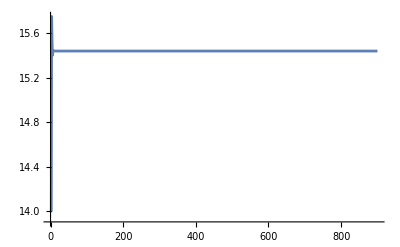

```mathematica
ListLinePlot[Table[aK[[n]]/bK[[n]], {n,1,900}]]
```

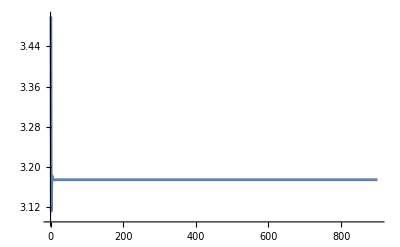

```mathematica
ListLinePlot[N[Table[aK[[n]]/cK[[n]], {n,1,900}]]]
```

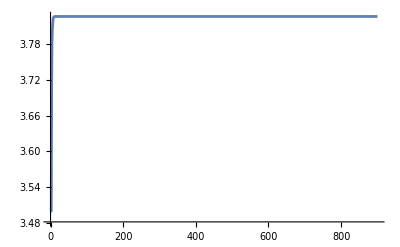

```mathematica
ListLinePlot[N[Table[aK[[n]]/xK[[n]], {n,1,900}]]]
```

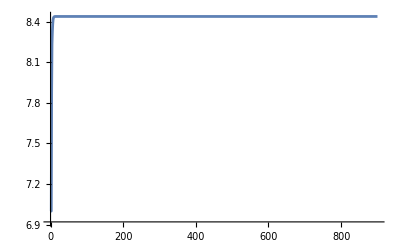

```mathematica
ListLinePlot[N[Table[aK[[n]]/yK[[n]], {n,1,900}]]]
```

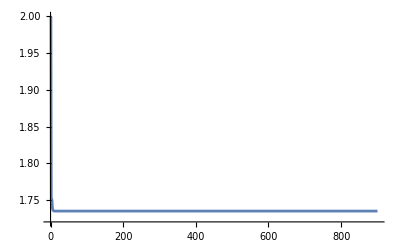

```mathematica
ListLinePlot[N[Table[aK[[n]]/zK[[n]], {n,1,900}]]]
```

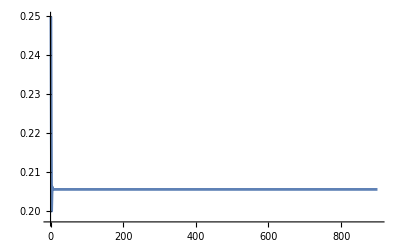

```mathematica
ListLinePlot[N[Table[bK[[n]]/cK[[n]], {n,1,900}]]]
```

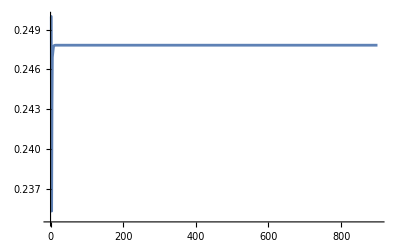

```mathematica
ListLinePlot[N[Table[bK[[n]]/xK[[n]], {n,1,900}]]]
```

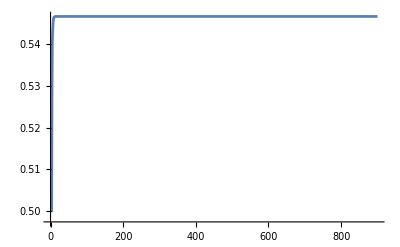

```mathematica
ListLinePlot[N[Table[bK[[n]]/yK[[n]], {n,1,900}]]]
```

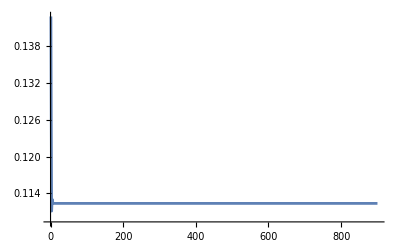

```mathematica
ListLinePlot[N[Table[bK[[n]]/zK[[n]], {n,1,900}]]]
```

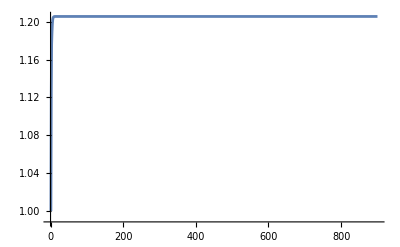

```mathematica
ListLinePlot[N[Table[cK[[n]]/xK[[n]], {n,1,900}]]]
```

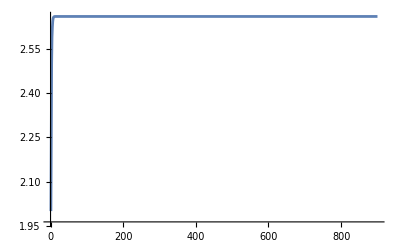

```mathematica
ListLinePlot[N[Table[cK[[n]]/yK[[n]], {n,1,900}]]]
```

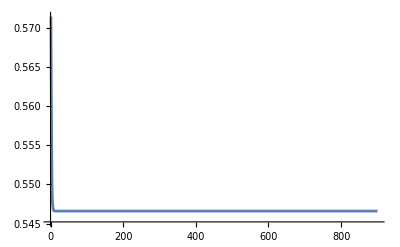

```mathematica
ListLinePlot[N[Table[cK[[n]]/zK[[n]], {n,1,900}]]]
```

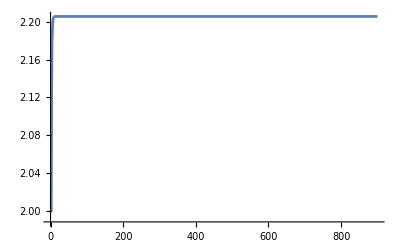

```mathematica
ListLinePlot[N[Table[xK[[n]]/yK[[n]], {n,1,900}]]]
```

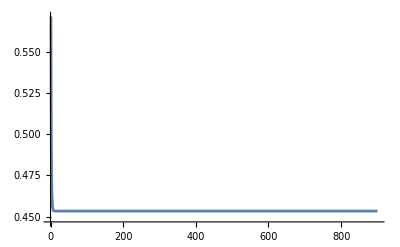

```mathematica
ListLinePlot[N[Table[xK[[n]]/zK[[n]], {n,1,900}]]]
```

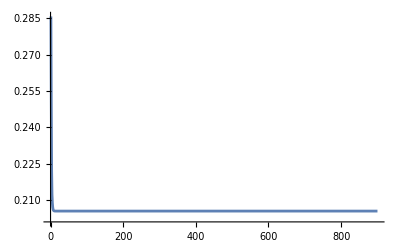

```mathematica
ListLinePlot[N[Table[yK[[n]]/zK[[n]], {n,1,900}]]]
```